```mathematica
alpha:=1/137;Mz:=92;thetaw:=0.23120;
F1:=Function[{kaa,kgg,lambda},8*(kgg/kaa)^2*alpha/12*Mz^5*thetaw*kaa^2*1/lambda^2][-0.254,0.217,x];F2:=Function[{kaa,kgg,lambda},8*(kgg/kaa)^2*alpha/12*Mz^5*thetaw*kaa^2*1/lambda^2][-0.333,0.054,x];F3:=Function[{kaa,kgg,lambda},8*(kgg/kaa)^2*alpha/12*Mz^5*thetaw*kaa^2*1/lambda^2][-0.340,-0.108,x];F4:=Function[{kaa,kgg,lambda},8*(kgg/kaa)^2*alpha/12*Mz^5*thetaw*kaa^2*1/lambda^2][0.010,-0.108,x];F5:=Function[{kaa,kgg,lambda},8*(kgg/kaa)^2*alpha/12*Mz^5*thetaw*kaa^2*1/lambda^2][0.095,0.217,x];
```

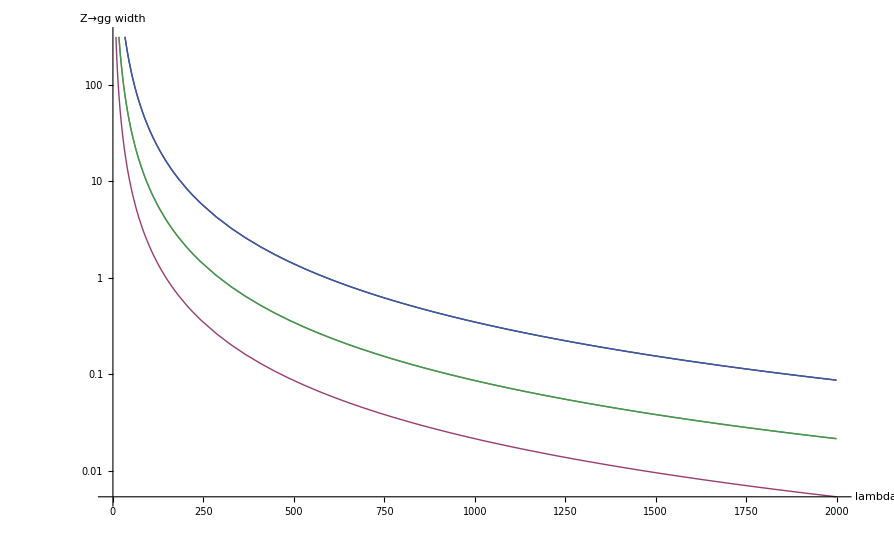

```mathematica
LogPlot[{F1,F2,F3,F4,F5},{x,0,2000},AxesLabel->{"lambda","Z→gg  width"}]
```

```mathematica
Short[Table[{lambda[kgg,w],kgg},{kgg,-0.1,1,0.001}],2]
```

{{16.5994 (1/w)^(1/4),-0.1},{16.5162 (1/w)^(1/4),-0.099},«1098»,{52.4918 (1/w)^(1/4),1.}}

```mathematica
sinwb2=0.23120;mz=91.1876;alpha=1/128;
lambda=(8/12*(#1^2)*alpha*(mz^5)*sinwb2*1/#2)^(1/4)&;
line=Table
kplot=ListPlot[Table[{lambda[kgg,#],kgg},{kgg,-0.1,1,0.001}],
AxesLabel->{Λ  [GeV],Subscript[K,gg]},
Filling->Axis,
Joined->True,
AxesStyle->Directive[Black,20],
AxesOrigin->{0,-0.1},
Frame->True]&;
maxplot=ListPlot[{{lambda[0.2,#],-0.1},{lambda[0.2,#],0.2}},
Joined->True]&;
textplotmin=Text["Λ < "#,{0,0.9}]&;
textplotusik=Text["Δ Γ = "#,{0,0.8}]&; 
Manipulate[Graphics[{kplot[w],maxplot[w],textplotmin[lambda[0.2,w]],textplotusik[w]}],{w,0.001,0.003}]
```

Table

```mathematica
(**)
```

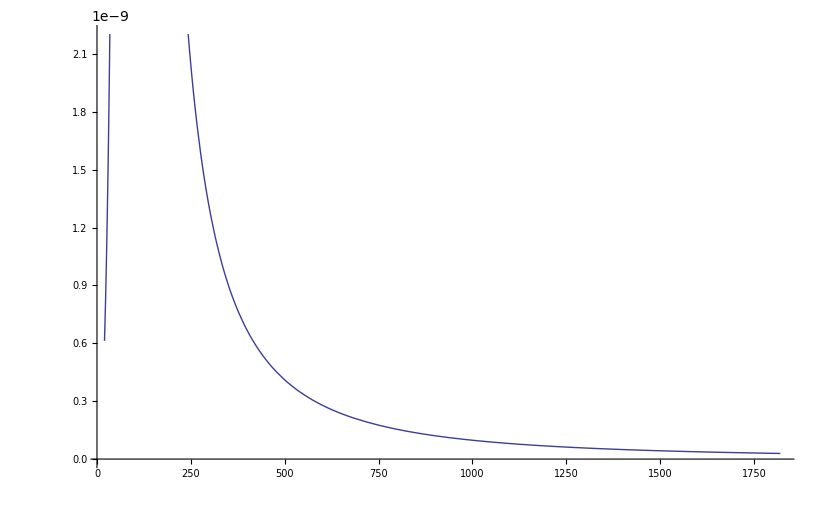

```mathematica
Zwidthfull:=2.4952;Zwidthfracmu:=0.03366;Zwidthfracuc:=0.101;Zwidthfracdsb:=0.166;Zmass:=91.1876;
Plot[12*Pi/Zmass^2 * Zwidthfracmu*Zwidthfracuc*x^2*Zwidthfull^2/((x^2-Zmass^2)^2 + x^4*Zwidthfull^2/Zmass^2),{x,20,1820}]
```

```mathematica
alphazmass:=1/128;sinw:=0.480832611;cosw:=0.876740947;Kgg:=0.2;lambda:=200;
```

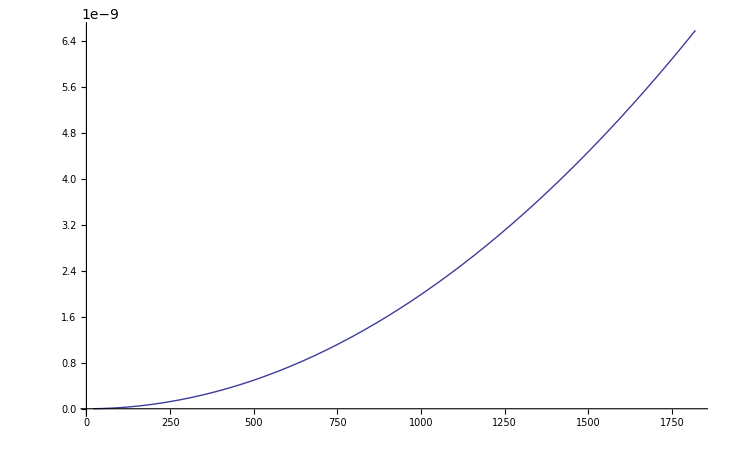

```mathematica
Plot[32*Pi/12*sinw^2/(sinw^2*cosw^2)*alphazmass^2*(1/2-(2/3)*sinw^2)^2*Kgg^2*x^2/lambda^4,{x,20,1820}]
```

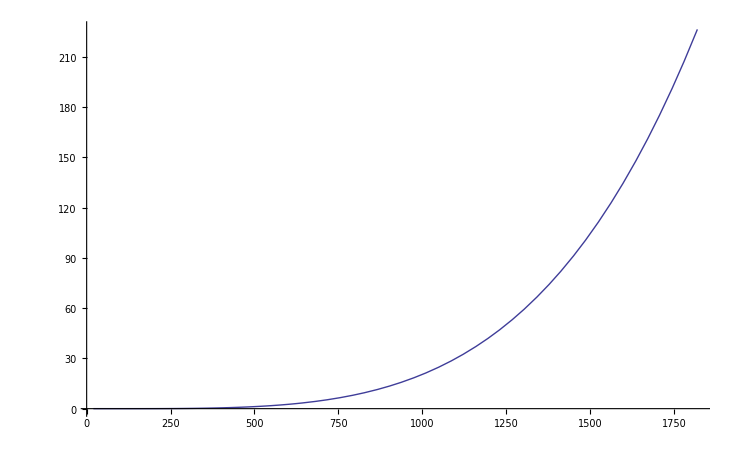

```mathematica
Plot[(32*Pi/12*sinw^2/(sinw^2*cosw^2)*alphazmass^2*(1/2-(2/3)*sinw^2)^2*Kgg^2*x^2/lambda^4)/(12*Pi/Zmass^2 * Zwidthfracmu*Zwidthfracuc*x^2*Zwidthfull^2/((x^2-Zmass^2)^2 + x^4*Zwidthfull^2/Zmass^2)),{x,20,1820}]
```